# Analysis of Senate Voting Networks

-Graphics-

U.S. Senate voting records have existed since 1789 and are constantly updated every day, however for the average U.S. citizen reading mounds of “yeas” and “nays” often results in little understanding of our complex legislative organization. By processing voting data, we can visualize connections between senators that have similarities in their voting. By visualizing this data, we can examine trends in senate polarization, party centralization, and faction formation. Extending the same methods used in this project to foreign voting records can also help us isolate independent and swing voters that are more easily influenced, and therefore targets for the U.S. government.

## Introduction

The U.S. Senate has been a imperative part of the United States’ legislative branch for nearly 236 years. Each year, the body of 100 people vote on thousands of issues that pertain to the lives of millions of Americans. Many today regard the body as a bipartisan network, however with further analysis we can examine the smaller, stronger coalitions that exist within each party. At the same time, visualizing these networks can help us isolate those that remain on the peripheries of each group and are more likely to be roped into other factions as swing voters. In this project, we will examine the trends and alliances within the U.S. Senate through its voting records.

## Setting Up Data and Functions

Here we import the data of voting records for US senators from 2024-2025 118th to 119th congress. 99 votes, All 1s (Yeas), 6s (Nays), and 9s (No vote). In addition we are importing the data that lists the political party and state of each senator from 2001 to 2025.

```mathematica
voteData=CloudGet[["https://www.wolframcloud.com/obj/3e76c447-68df-41c9-8e06-de7547e73f78"](https://www.wolframcloud.com/obj/3e76c447-68df-41c9-8e06-de7547e73f78)];
```

```mathematica
partyData = CloudGet[["https://www.wolframcloud.com/obj/ae6420d3-afe3-455a-999a-8672feb7b071"](https://www.wolframcloud.com/obj/ae6420d3-afe3-455a-999a-8672feb7b071)];
```

```mathematica
dataRows = Rest[partyData];
```

```mathematica
partyLookup=AssociationThread@@Transpose[dataRows];
```

Adding the remaining senators that were elected before 2001.

```mathematica
AssociateTo[partyLookup,"Charles Schumer" -> "D-NY"];
AssociateTo[partyLookup, "Michael Crapo"->"R-ID"];
AssociateTo[partyLookup,"Richard Durbin"->"R-IL"];
AssociateTo[partyLookup,"Susan Collins"->"R-ME"];
AssociateTo[partyLookup,"Addison McConnell"->"R-KY"];
AssociateTo[partyLookup,"Charles Grassley"->"R-IA"];AssociateTo[partyLookup,"Ronald Wyden"->"D-OR"];AssociateTo[partyLookup,"John Reed"->"D-RI"];AssociateTo[partyLookup,"Patricia Murray"->"D-WA"];
```

This is the function that we will be using to turn the data we imported into a clear network graph. First, we take a dataset of the original .csv file containing the names and voting records of the senators, and remove the headers. Then, we reformat all of the names into a new column, and with the new dataset, generate a list of all possible pairs. This amounts to 4950 combinations. Each pair is then examined in the findEdges function. Once we get the list of edges returned, we can graph our final network, with each node being a senator and each edge being a connection of political similarity. The parameter noSwings is a boolean that establishes whether or not we want to display the “swing” voters in our final graph, or rather the people that do not belong to a faction.

Function to visualize the raw voting data file into a voting network.

```mathematica
visualizeVotingData[data_,threshold_,noSwings_]:=Module[{headers = First[data],dataRows,table,pairs,edges,ds,newNames,newDS,vertices,dataRows2},
dataRows =Rest[data];
table = DeleteColumns[AssociationThread[headers,#]&/@dataRows,"icpsr"];
ds= Dataset[table];
newNames = reformatName[#]&/@Normal[ds[All,"name"]];
dataRows2=MapThread[Append,{Rest[data],newNames}];
pairs=Subsets[dataRows2,{2}];
edges = findEdges[pairs,threshold];
(*re-format existing LASTNAME, firstname middlename to a Firstname Lastname Party-State way, then let all of the names *)
If[noSwings ==True,Graph[edges,VertexLabels->Placed["Name",Tooltip]],Graph[newNames,edges,VertexLabels->Placed["Name",Tooltip]]]]
```

voteMatchCount is a function that essentially compares the two lists passed in as arguments. It should return the number of matches. This is how we will compare the voting records between two senators.

```mathematica
voteMatchCount[v1_,v2_]:=Module[{count=0},Do[If[v1[[i]]== v2[[i]],count=count+1],{i,1,Length[v1]}];count];
```

Here we will draw the edges of the graph. The “similarity threshold” is the number of matches between two senators’ votes. In defining edges, we only want to make an edge if the two senators have some voting similarity. Otherwise we would end up with a shape the looks like a circle, since most of the senators have voted the same as every other senator on at least 1 issue.  

As we lower the similarity threshold, we will see a decrease in modularity. For now, we will set the similarityThreshold to 15. This should draw an edge to any senators that have voted the same on at least 15 issues. In defining edges, we are taking the names of both the senators from our list of pairs (remember it is a 2D array) and both of their votes. (pairs[i,1,5;;] should return all of the remaining votes that will just be an array of {1,6,1,9,1,....} 99 times. We can compare each of the pairs in the senator pairs list by applying this function. Then, compare the number that was returned with our similarityThreshold which in this case is 10. If the number of similar votes is greater than or equal to 10, then we construct an edge between the two senators.

Function that checks for commonalities in voting given a list of pairs of senators, and returns a list of all the edges between the senators.

```mathematica
findEdges[pairs_,threshold_]:=Module[{edges,name1,votes1,name2,votes2,matches},edges=Table[name1=pairs[[i,1,-1]];votes1=Drop[pairs[[i,1,5;;]],-1];name2=pairs[[i,2,-1]];votes2=Drop[pairs[[i,2,5;;]],-1];matches=voteMatchCount[votes1,votes2];
If[matches>=threshold,UndirectedEdge[name1,name2],Null],{i,Length[pairs]}];
DeleteCases[edges,Null]]
```

This function that takes in a string formatted “LASTNAME, Firstname Middlename (Nickname)” and just returns “Firstname Lastname - PARTY-STATE” abbrev.

```mathematica
reformatName[name_]:=Module[{newName},newName=StringJoin[StringSplit[name,{" ",","}][[3]]," ",Capitalize[ToLowerCase[StringSplit[name,{" ",","}][[1]]]]];If[KeyExistsQ[partyLookup,newName],newName=StringJoin[newName," ",Lookup[partyLookup,newName]],newName]]
```

This is an example of what it does to the names in the dataset.

```mathematica
reformatName["ALSOBROOKS, Angela"]
```

Angela Alsobrooks D-MD

## Exploring Variance in Party Centralization

This is what our network of senators should look like if we draw an edge between every senator that had at least 15 votes in common out of our sample of 99 votes. As expected, a group of two clusters formed, with each cluster representing one political party.

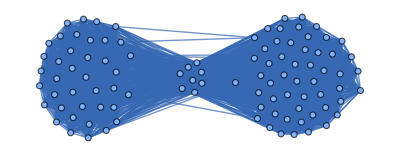

```mathematica
visualizeVotingData[voteData,15,True]
```

Here we are going to generate a list of graphs that contain gradually increasing thresholds of similarity, then create a Manipulate that iterates through these graphs to visualize the affect of the similarity threshold. As we increase our threshold of matched votes, we can isolate the body of senators into two political factions. As we increase our threshold even more, we can observe that there is not necessarily an equal distribution of decentralization, with the Democratic party’s network being relatively more spread out than the Republican’s. At the same time, we can see even smaller, more centralized groups clearly within our larger Republican and Democratic networks. The nodes that lie along the ends of the graph are the senators that no longer share a similar voting pattern to anyone else, and therefore cannot form an edge.

Create a table of all the graphs with gradually increasing thresholds of similarity.

```mathematica
graphs = Parallelize[Table[visualizeVotingData[voteData,i,False],{i,1,98,1}]];
```

Manipulate that shows the effect of changing the similarityThreshold variable in the voting networks.

```mathematica
Manipulate[graphs[[similarity]],{similarity,15,98,1}]
```

Let’s isolate this graph, where we can see that our current Senate has an more centralized Republican majority, and decentralized Democrat minority.

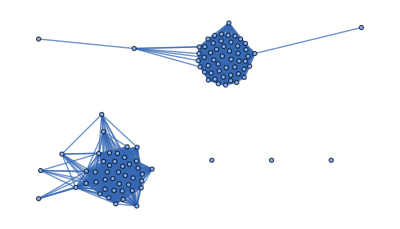

```mathematica
visualizeVotingData[voteData,80,False]
```

Let’s contrast this graph with the voting network just a few months before.

Below we can observe that before the 2024 election, Republicans were generally more decentralized than Democrats. During this time, Democrats were the majority party and Republicans were the minority.

```mathematica
voteData2= Import["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set11.csv"]; (*from 1/31/2024 to 4/30/2024*)
```

```mathematica
visualizeVotingData[voteData2,80,True];
```

The 116th congress had a Republican majority from 2019 to 2021, the 117th and 118th congress had Democratic majority from 2021-2025, and the 119th congress has a Republican majority for 2025 to 2026. We notice that every time a party holds the majority in senate, they become more centralized, and their political counterparts become more an more decentralized. This further emphasizes the importance of holding majority in congress, because parties are not just able to have more people from their own party, but also control and sway the opinions of opposing members as well.

We can observe party centralization overtime. Here I define a list of dates that correspond to all of the datasets represented in the visuals on the graph.

```mathematica
dates = {"3/12/2020 to 9/20/2020","9/20/2020 to 1/20/21","1/20/2021 to 6/8/2021","6/8/2021 to 8/21/2021","8/21/2021 to 12/09/2021","12/13/2021 to 4/27/2022","4/27/2022 to 12/15/2022","12/15/2022 to 4/27/2023","9/7/2023 to 12/06/2023","1/31/2024 to 4/30/2024","4/30/2024 to 9/30/2024","9/30/2024 to 7/4/2025"};
```

Here I create a table to create the graphs that show party centralization overtime.

```mathematica
CloudPut["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set1.csv"]
```

CloudObject[https://www.wolframcloud.com/obj/a588a4df-8336-4a67-bb92-a66d86305b87]

```mathematica
ClearAll[partyCentralization]
```

```mathematica
AppendTo[partyCentralization,Import
```

```mathematica
partyCentralization = Table[visualizeVotingData[Import[StringJoin["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set",ToString[i],".csv"]],80,True],{i,1,12}];
```

Here I create a manipulate to show the graphs from the partyCentralization table.

```mathematica
Manipulate[Column[{Show[partyCentralization[[time]],ImageSize->Large],Grid[{{"date:",dates[[time]]}}]}],{time,1,12,1}]
```

Part::partd: Part specification partyCentralization⟦8⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

## Alliances and Factions Within the U.S. Senate

When we increased our similarity threshold, we saw an increase of modularity within our voting network. Here, we will further explore the extent to which we can analyze a presumably bipartisan network for smaller factions given individual voting records from 9/7/2023 to 12/06/2023.  Increase the “similarity” variable to break up the network into even smaller factions.

Import voting data from 9/7/2023 to 12/06/2023

```mathematica
voteData9 = Import["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set9.csv"];(*from 9/7/2023 to 12/06/2023*)
```

Draw the graphs for each similarity threshold of the voting data. Total of 99 graphs. CommunityGraphPlot should highlight the communities found within the network.

```mathematica
graphs9 = Parallelize[Table[CommunityGraphPlot[visualizeVotingData[voteData9,i,False]],{i,1,99,1}]];
```

Draw manipulate that iterates through the visualizations.

```mathematica
Manipulate[graphs9[[similarity]],{similarity,1,99,1}]
```

Part::partd: Part specification graphs9⟦73⟧ is longer than depth of object.

Part::partd: Part specification graphs9[[73]] is longer than depth of object.

Isolate the graph for the voting data when the similarity threshold was 88.

```mathematica
CommunityGraphPlot[visualizeVotingData[voteData9,88,False]]
```

-Graphics-

Let’s isolate this frame. Here, we can see high modularity. The dots that are on their own are the senators that tend to vote on their own and are not necessarily confined to a faction. This can be crucial to identify in voting systems both in the U.S. Senate and foreign governments, as swing voters can be more willing to change opinions and cooperate with other political forces.  In addition it can be important for voters to understand where their candidates lie on each political faction.

There are a total of 20 committees in the U.S. Senate, each designed to tackle different categories of legislation. The committees that each senator is affiliated with largely influences how they vote, as they often sponsor bills with other senators in their committee. Therefore understanding the common committees between senate factions can help us understand why certain senators have similar voting patterns. Here I am importing data on all of the current Senate committee membership. In the .csv file, the data is formatted such that you see the name of the committee as a header and underneath a list of all of the members. I reformat it so that I have an association with all of the Senate members and the committees they are in. 

Before: “SSAF”→{{“name”→”John Boozman”,”party”→”majority”,”rank”→1,”title”→”Chairman”,”bioguide”→”B001236”}...}
After: John Boozman→{SSAF,SSAP,SSEV,SSRA,SSVA,JCSE}...

In the file, the senators are associated to only the abbreviated versions of committees, so I need another file to associate the abbreviated names to their full names. (EX: SSAP → Senate Committee on Appropriations).

Code to import and reformat the information on Senate committees and membership.

```mathematica
committees = Import["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\committees-current.csv"];
committeesRest = committees[[23;;]];
membership = Import["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\committee-membership-current.json"];
committeesNames = AssociationThread[Table[committeesRest[[i]][[5]],{i,1,Length[committeesRest]}],
Table[committeesRest[[i]][[2]],{i,1,Length[committeesRest]}]];
membersEach = Table[Table[membership[[i]][[2]][[x]][[1]][[2]],{x,1,Length[membership[[i]][[2]]]}],{i,1,Length[membership]}][[;;98]];
senateMembers =DeleteDuplicates[Flatten[membersEach]];
senateCommittees = Table[membership[[i]][[1]],{i,1,Length[membership]}][[;;98]];(*only till the 98th item so we don't get the House Committees*)
senatorsToCommittees = AssociationThread[senateCommittees,membersEach];
```

Here I take in a 2D array of the groups, then see the top two most common committees amongst the group. I do this by iterating through the list of all of the names in each group that is in senatorGroups and looking up the name on my senatorsAndCommittees Association. I then append all of the names found from the Association for each senator, then see what is the most common committee between all of them.

```mathematica
senatorsAndCommittees =AssociationThread[senateMembers,Table[DeleteDuplicates[DeleteCases[Table[If[ContainsAny[senatorsToCommittees[key],{name}],StringTake[key,4]],{key,Keys[senatorsToCommittees]}],Null]],{name,senateMembers}]];
```

```mathematica
findCommonInterest[senatorGroups_]:=Module[{},Table[StringJoin[Riffle[Commonest[DeleteCases[Flatten[Table[If[KeyExistsQ[senatorsAndCommittees,StringReplace[name,RegularExpression[" \\S-\\S*"]->""]],StringDelete[Lookup[committeesNames,Lookup[senatorsAndCommittees,StringReplace[name,RegularExpression[" \\S-\\S*"]->""]]],"Senate Committee on "]],{name,group}]],Null],UpTo[2]],"\n"]],{group,senatorGroups}]]
```

Now, we can use the function findCommonInterest to label our graph! Each label should consist of the top two committees for each of the networks separated by a newline.

```mathematica
CommunityGraphPlot[visualizeVotingData[voteData9,88,True],CommunityLabels->findCommonInterest[FindGraphCommunities[visualizeVotingData[voteData9,88,True]]]]
```

-Graphics-

Here is another example with voting data from 6/8/2021 to 8/21/2021. Here we see a clear divide within the Democratic party.

```mathematica
CommunityGraphPlot[visualizeVotingData[Import["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set7.csv"],96,True],CommunityLabels->findCommonInterest[FindGraphCommunities[visualizeVotingData[Import["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set7.csv"],96,True]]]]
```

-Graphics-

Here is a Table of all of all data visualizations of the factions within senate over time. By keeping the similarity threshold to 96, we can isolate the voting groups that are more consistent.

```mathematica
partyFactions = Table[CommunityGraphPlot[visualizeVotingData[Import[StringJoin["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set",ToString[i],".csv"]],96,True],CommunityLabels->findCommonInterest[FindGraphCommunities[visualizeVotingData[Import[StringJoin["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\datasets\\set",ToString[i],".csv"]],96,True]]]],{i,1,12}];
```

```mathematica
Manipulate[Column[{Show[partyFactions[[time]],ImageSize->Medium],Grid[{{"date:",dates[[time]]}}]}],{time,1,12,1}]
```

## Locate a Senator

This is a function that highlights the senator of the user’s choice.

```mathematica
ColorSenator[graph_Graph,vertex_,color_:Red]:=Module[{style},style=VertexStyle->{vertex->color};
Graph[VertexList[graph],EdgeList[graph],style,Sequence@@Options[graph]]]
```

Display the graph.

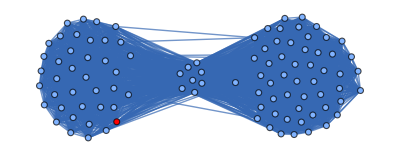

```mathematica
ColorSenator[visualizeVotingData[voteData,15,True],"Mazie Hirono",Red]
```

## Conclusions

## Reference

https://github.com/unitedstates/congress-legislators/blob/main/committee-membership-current.yaml - committee stuff
https://voteview.com/ - voting records
https://www.senate.gov/senators/NewSenators.htm - list of senator parties
https://legiscan.com/US
https://christopherwolfram.com/projects/voting-modularity/
Michels, Lars & Koirala, Nabin & Groppa, Sergiu & Luechinger, Roger & Gantenbein, Andreas & Sandor, Peter & Kollias, Spyros & Riederer, Franz & Muthuraman, Muthuraman. (2021). Structural brain network characteristics in patients with episodic and chronic migraine. The Journal of Headache and Pain. 22. 10.1186/s10194-021-01216-8.

```mathematica
ResourceFunction["SaveReadableNotebook"]["C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\WSRP Vote Records DAY2.nb","C:\\Users\\schoo\\Documents\\Wolfram\\WSRP Project\\WSRP Vote Records (readable).nb"]
```

File[C:\Users\schoo\Documents\Wolfram\WSRP Project\WSRP Vote Records (readable).nb]